```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3/datav4

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,870,960,5}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,870,960,5}];
r422=chi4/chi2;
(*r422[[1]]=r422[[1]][[17;;-1]];*)
(*Export["r42data_tosmooth.dat",r422]*)
```

```mathematica
Dimensions[r422]
```

{19,331}

```mathematica
mub=Table[i,{i,870,960,5}];
T=Table[i,{i,17,50,0.1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r422[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
(*Export["r42high.dat",R42all]*)
```

```mathematica
Length[chi2[[2]]]
```

331

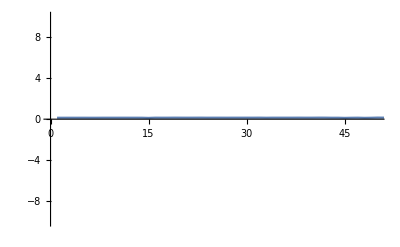

```mathematica
ListLinePlot[r422[[15]],PlotRange->{{0,50},{-10,10}}]
```

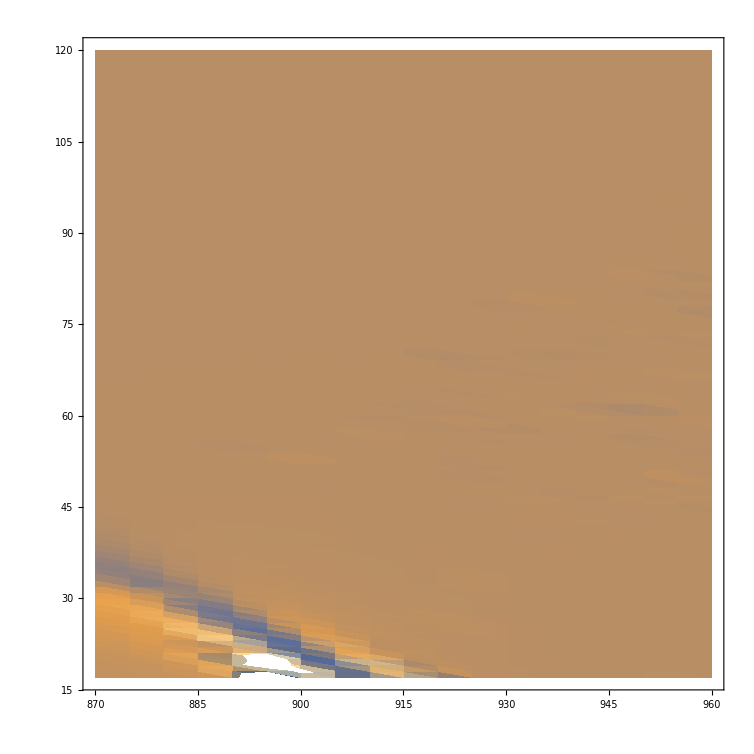

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-25,40}}]
```

```mathematica
ListLinePlot[{Transpose[{T,r422[[1]]}]},PlotRange->{All,{-10,12}}]
```

Transpose::nmtx: {{17,18,19,20,21,22,23,24,25,26,«94»},{-0.324235,-1.15771,-0.199564,1.03484,1.00453,1.00066,1.00132,1.00329,1.00848,1.0191,«110»}} 的前两层无法转置.

Transpose::nmtx: {{17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,«94»},{-0.324235,-1.15771,-0.199564,1.03484,1.00453,«18»,1.00132,1.00329,1.00848,1.0191,«110»}} 的前两层无法转置.

Transpose::nmtx: {{17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,«94»},{-0.324235,-1.15771,-0.199564,1.03484,1.00453,1.00066,1.00132,1.00329,1.00848,1.0191,«110»}} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

-Graphics-